```mathematica
question 1
```

```mathematica
General Solutions of 1^st and 2^nd order Partial Differential Equations
```

```mathematica
Ques 1:Find General Solution of Partial Differential Equation 
		x D[u[x,y], x] + y D[u[x,y], y] = 2xy .
```

```mathematica
pde=x* D[u[x,y],x]+y*D[u[x,y],y]==2*x*y;
sol=DSolve[pde,u[x,y],{x,y}];
Print["General Solution of given Partial Differential Equation is : ",sol]
```

General Solution of given Partial Differential Equation is : {{u[x,y]→x y+C[1][y/x]}}

```mathematica
Ques 2:Find General Solution of Partial Differential Equation 
		3 D[u[x,y], x] + 2 D[u[x,y], y] = 0 .
```

```mathematica
pde=3*D[u[x,y],x]+2*D[u[x,y],y]==0;
sol=DSolve[pde,u[x,y],{x,y}];
Print["General Solution of given Partial Differential Equation is : ",sol]
```

General Solution of given Partial Differential Equation is : {{u[x,y]→C[1][1/3 (-2 x+3 y)]}}

```mathematica
Ques 3:Find General Solution of Partial Differential Equation 
Subscript[u, x] + Subscript[xu, y] = 0.
```

```mathematica
pde=D[u[x,y],x]+x*D[u[x,y],y]==0;
sol=DSolve[pde,u[x,y],{x,y}];
Print["General Solution of given Partial Differential Equation is : ",sol]
```

General Solution of given Partial Differential Equation is : {{u[x,y]→C[1][1/2 (-x^2+2 y)]}}

```mathematica
Ques 4:Find General Solution of Partial Differential Equation 
Subscript[u, tt] =Subscript[u, xx] .
```

```mathematica
pde=D[u[x,t],{t,2}]==D[u[x,t],{x,2}];
sol=DSolve[pde,u[x,t],{x,t}];
Print["General solution of given Partial Differential Equation is : ",sol]
```

General solution of given Partial Differential Equation is : {{u[x,t]→C[1][t-x]+C[2][t+x]}}

```mathematica
Ques 5:Find General Solution of Partial Differential Equation 
Subscript[u, tt] =9 Subscript[u, xx] .
```

```mathematica
pde=D[u[x,t],{t,2}]==9*D[u[x,t],{x,2}];
sol=DSolve[pde,u[x,t],{x,t}];
Print["General Solution of given Partial Differential Equation is : ",sol]
```

General Solution of given Partial Differential Equation is : {{u[x,t]→C[1][t-x/3]+C[2][t+x/3]}}

```mathematica
Ques 6:Find General Solution of Partial Differential Equation 
Subscript[u, tt] =4 Subscript[u, xx] .
```

```mathematica
pde=D[u[x,t],{t,2}]==4*D[u[x,t],{x,2}];
sol=DSolve[pde,u[x,t],{x,t}];
Print["General Solution of given Partial Differential Equation is : ",sol]
```

General Solution of given Partial Differential Equation is : {{u[x,t]→C[1][t-x/2]+C[2][t+x/2]}}

```mathematica
Quit
```

## question 2

```mathematica
Q1.Solve the Cauchy problem Subscript[u, x] +Subscript[xu, y]=y,u(0,y)=y^2 and plot the solution also.
```

```mathematica
pde=D[u[x,y],x]+x*D[u[x,y],y]==y;
sol=DSolve[{pde,u[0,y]==y^2},u[x,y],{x,y}];
Print["solution of given cauchy problem is: ",sol]
Plot3D[u[x,y]/.sol,{x,-3,3},{y,-5,5},AxesLabel->{x,y,u}]
```

solution of given cauchy problem is: {{u[x,y]→1/12 (-4 x^3+3 x^4+12 x y-12 x^2 y+12 y^2)}}

```mathematica
Q2.Solve the Cauchy problem Subscript[u, x] +Subscript[u, y]=1,u(x,0)=x^2 and plot the solution also.
```

```mathematica
pde=D[u[x,y],x]+D[u[x,y],y]==1;
sol=DSolve[{pde,u[x,0]==x^2},u[x,y],{x,y}];
Print["solution of given cauchy problem is: ",sol]
Plot3D[u[x,y]/.sol,{x,-3,3},{y,-5,5},AxesLabel->{x,y,u}]
```

solution of given cauchy problem is: {{u[x,y]→x^2+y-2 x y+y^2}}

```mathematica
Q3.Solve the Cauchy problem Subscript[u, x] +Subscript[xu, y]=0,u(0,y)=siny and plot the solution also.
```

```mathematica
pde=D[u[x,y],x]+x*D[u[x,y],y]==0;
sol=DSolve[{pde,u[0,y]==Sin [y]},u[x,y],{x,y}];
Print["solution of given cauchy problem is: ",sol]
Plot3D[u[x,y]/.sol,{x,-4,4},{y,-6,6},AxesLabel->{x,y,u}]
```

solution of given cauchy problem is: {{u[x,y]→Sin[1/2 (-x^2+2 y)]}}

-Graphics3D-

```mathematica
Q4.Solve the Cauchy problem Subscript[yu, x] +Subscript[xu, y]=0,u(0,y)=Exp[-y^2]and plot the solution also.
```

```mathematica
pde=y*D[u[x,y],x]+x*D[u[x,y],y]==0;
sol=DSolve[{pde,u[0,y]==Exp[-y^2]},u[x,y],{x,y}];
Print["solution of given cauchy problem is: ",sol]
Plot3D[u[x,y]/.sol,{x,-4,4},{y,-6,6},AxesLabel->{x,y,u}]
```

solution of given cauchy problem is: {{u[x,y]→ⅇ^(x^2-y^2)}}

-Graphics3D-

```mathematica
Q5.Solve the Cauchy problem Subscript[u, x] +2 Subscript[u, y]=0,u(x,0)=sin x and plot the solution also.
```

```mathematica
pde=D[u[x,y],x]+2*D[u[x,y],y]==0;
sol=DSolve[{pde,u[x,0]==Sin [x]},u[x,y],{x,y}];
Print["solution of given cauchy problem is: ",sol]
Plot3D[u[x,y]/.sol,{x,-4,4},{y,-6,6},AxesLabel->{x,y,u}]
```

solution of given cauchy problem is: {{u[x,y]→Sin[1/2 (2 x-y)]}}

-Graphics3D-

```mathematica
Q5.Solve the Cauchy problem (1+x^2)Subscript[u, x] +Subscript[xu, y]=y,u(x,0)=sin x and plot the solution also.
```

```mathematica
pde=(1+x^2)*D[u[x,y],x]+x*D[u[x,y],y]==0;
sol=DSolve[{pde,u[0,y]==y},u[x,y],{x,y}];
Print["solution of given cauchy problem is: ",sol]
Plot3D[u[x,y]/.sol,{x,-4,4},{y,-6,6},AxesLabel->{x,y,u}]
```

solution of given cauchy problem is: {{u[x,y]→1/2 (2 y-Log[1+x^2])}}

-Graphics3D-

```mathematica
Quit
```

## question 3

```mathematica
Plotting the characteristic curve for first order PDE
```

```mathematica
Q1. Plot the characteristic curves of first orde PDE: Subscript[u, x] - Subscript[u, y]=1
```

```mathematica
pde= D[u[x,y],x]-D[u[x,y],y]==1;
sol=DSolve[pde,u[x,y],{x,y}]
```

{{u[x,y]→x+C[1][x+y]}}

```mathematica
f0=ContourPlot3D[u-x,{u,0,1},{x,0,1},{y,0,1},ImageSize-> {250,250},AxesLabel-> {"x","y","u"}];
f1=ContourPlot3D[x+y,{u,0,1},{x,0,1},{y,0,1},ImageSize-> {250,250},AxesLabel-> {"x","y","u"}];
Print[f0,f1]
```

-Graphics3D--Graphics3D-

```mathematica
Q2. Plot the characteristic curves of first orde PDE:(1+x^2)Subscript[u, x]+Subscript[u, y] =0.
```

```mathematica
pde=(1+x^2)*D[u[x,y],x]+D[u[x,y],y]==0;
sol=DSolve[pde,u[x,y],{x,y}]
```

{{u[x,y]→C[1][y-ArcTan[x]]}}

```mathematica
f0=ContourPlot3D[u-0,{u,0,1},{x,0,1},{y,0,1},ImageSize-> {250,250},AxesLabel-> {"x","y","u"}];
f1=ContourPlot3D[y-ArcTan[x],{u,0,1},{x,0,1},{y,0,1},ImageSize-> {250,250},AxesLabel-> {"x","y","u"}];
Print[f0,f1]
```

-Graphics3D--Graphics3D-

```mathematica
Q3. Plot the characteristic curves of first orde PDE:Subscript[xu, x]+Subscript[yu, y] =2xy.
```

```mathematica
pde=x*D[u[x,y],x]+y*D[u[x,y],y]==2*x*y;
sol=DSolve[pde,u[x,y],{x,y}]
```

{{u[x,y]→x y+C[1][y/x]}}

```mathematica
f0=ContourPlot3D[u-x*y,{u,0,2},{x,0,1},{y,0,2},ImageSize-> {250,250},AxesLabel-> {"x","y","u"}];
f1=ContourPlot3D[y/x,{u,-1,2},{x,0.1,0.5},{y,-1,2},ImageSize-> {250,250},AxesLabel-> {"x","y","u"}];
Print[f0,f1]
```

-Graphics3D--Graphics3D-

```mathematica
Q4. Plot the characteristic curves of first orde PDE:Subscript[xu, x]+(x+y)Subscript[u, y] =u+1.
```

```mathematica
pde=x*D[u[x,y],x]+(x+y)*D[u[x,y],y]==u[x,y]+1;
sol=DSolve[pde,u[x,y],{x,y}]
```

{{u[x,y]→-1+x C[1][(y-x Log[x])/x]}}

```mathematica
f0=ContourPlot3D[(u+1)/x,{u,-1,2},{x,0.1,0.5},{y,0,1},ImageSize-> {250,250},AxesLabel-> {"x","y","u"}];
f1=ContourPlot3D[(y-x*Log[x])/x,{u,0,1},{x,0.1,0.5},{y,0,1},ImageSize-> {250,250},AxesLabel-> {"x","y","u"}];
Print[f0,f1]
```

-Graphics3D--Graphics3D-

```mathematica
Q5. Plot the characteristic curves of first orde PDE:Subscript[xu, x]+Subscript[yu, y] =0.
```

```mathematica
pde=x*D[u[x,y],x]+y*D[u[x,y],y]==0;
sol=DSolve[pde,u[x,y],{x,y}]
```

{{u[x,y]→C[1][y/x]}}

```mathematica
f0=ContourPlot3D[u-0,{u,0,2},{x,0,1},{y,0,2},ImageSize-> {250,250},AxesLabel-> {"x","y","u"}];
f1=ContourPlot3D[y/x,{u,-1,2},{x,0.1,0.5},{y,-1,2},ImageSize-> {250,250},AxesLabel-> {"x","y","u"}];
Print[f0,f1]
```

-Graphics3D--Graphics3D-

```mathematica
Quit
```

```mathematica
vibrating string 4
```

```mathematica
Solution of vibrating string problem using D’Alembert formula with
initial conditions
```

```mathematica
Q1. Solve,Subscript[u, tt]=Subscript[u, xx], u(x,0)=0,Subscript[u, t](x,0)=x^2: x ∈ R, t>0
```

```mathematica
DSolve[D[u[x,t],{t,2}]==D[u[x,t],{x,2}],u[x,t],{x,t}]
```

{{u[x,t]→C[1][t-x]+C[2][t+x]}}

```mathematica
da[c_,f_,g_,x_,t_]:=
1/2((f/.x-> x+c*t)+(f/.x-> x-c*t))+1/(2*c)*Integrate[g,{x,x-c*t,x+c*t}]
da[1,0,x^2,x,t]
Plot3D[%,{t,1,8},{x,-8,8},AxesLabel-> {t,x,u}]
```

1/2 (-1/3 (-t+x)^3+1/3 (t+x)^3)

-Graphics3D-

```mathematica
Q2. Solve,Subscript[u, tt]=Subscript[u, xx], u(x,0)=Sin[x],Subscript[u, t](x,0)=Cos[x]: x ∈ R, t>0
```

```mathematica
DSolve[D[u[x,t],{t,2}]==D[u[x,t],{x,2}],u[x,t],{x,t}]
```

{{u[x,t]→C[1][t-x]+C[2][t+x]}}

```mathematica
da[c_,f_,g_,x_,t_]:=
1/2((f/.x-> x+c*t)+(f/.x-> x-c*t))+1/(2*c)*Integrate[g,{x,x-c*t,x+c*t}]
da[1,Sin[x],Cos[x],x,t]
Plot3D[%,{t,1,8},{x,-8,8},AxesLabel-> {t,x,u}]
```

Cos[x] Sin[t]+1/2 (-Sin[t-x]+Sin[t+x])

-Graphics3D-

```mathematica
Quit
```

```mathematica
heat equation 5
```

```mathematica
Solution of the heat equation Subscript[u, t]=Subscript[u, xx] with initial conditions.
```

```mathematica
Q1. Solve,Subscript[u, t]=0.5 Subscript[u, xx],u(x,0)=Sin^2 x,u(0,t)=0,u(π,t)=0,0<x<π,t>0
```

```mathematica
eqn={D[u[x,t],t]==1/2*D[u[x,t],{x,2}],u[x,0]==(Sin[x])^2,u[0,t]==0,u[π,t]==0};
sol=NDSolve[eqn,u[x,t],{x,0,π},{t,0,4}];
Plot3D[u[x,t]/.sol,{x,0,π},{t,0,4},AxesLabel-> {x,t,u}]
```

-Graphics3D-

```mathematica
Q2. Solve,Subscript[u, t]=4 Subscript[u, xx],u(x,0)=x^2-x^3,u(0,t)=0,u(1,t)=0,0<x<1,t>0
```

```mathematica
eqn={D[u[x,t],t]==4*D[u[x,t],{x,2}],u[x,0]==x^2-x^3,u[0,t]==0,u[1,t]==0};
sol=NDSolve[eqn,u[x,t],{x,0,1},{t,0,5}];
Plot3D[u[x,t]/.sol,{x,0,1},{t,0,5},AxesLabel-> {x,t,u}]
```

-Graphics3D-

```mathematica
Quit
```

```mathematica
dimensional wave eq 6
```

```mathematica
Solution of one-dimensional wave equation utt=c2 uxx with
initial conditions:
(i) u(x,0)=f(x),Subscript[u, t](x,0)=g(x):x ∈ R,t>0
      (ii) u(x,0)=f(x),Subscript[u, t](x,0)=g(x),u(0,t)=0:x∈R,t>0
     (iii)u(x,0)=f(x),Subscript[u, t](x,0)=g(x),u(0,t)=0:x ∈R,t>0
```

```mathematica
Q1.Solve, Subscript[u, tt]-Subscript[u, xx]=0,u(x,0)=3*Sin[x],Subscript[u, t](x,0)=x^4;0<x<1,t>0
```

```mathematica
eqn={D[u[x,t],{t,2}]-D[u[x,t],{x,2}]==0,u[x,0]==3*Sin[x],Derivative[0,1][u][x,0]==x^4};
sol=NDSolve[eqn,u[x,t],{x,0,1},{t,0,4}];
Plot3D[u[x,t]/.sol,{x,0,1},{t,0,4},AxesLabel-> {"t","x","u"},Ticks-> {{0,1,2,3,4},{0,1},{-3,0}}]
```

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable x. Artificial boundary effects may be present in the solution.

-Graphics3D-

```mathematica
Q2.Solve, Subscript[u, tt]-4 Subscript[u, xx]=0,u(x,0)=Subscript[Log, 10][x+1],Subscript[u, t](x,0)=x;0<x<1,
t>0
```

```mathematica
eqn={D[u[x,t],{t,2}]-4*D[u[x,t],{x,2}]==0,u[x,0]==Log10[x+1],Derivative[0,1][u][x,0]==x};
sol=NDSolve[eqn,u[x,t],{x,0,1},{t,0,4}];
Plot3D[u[x,t]/.sol,{x,0,1},{t,0,4},AxesLabel-> {"t","x","u"},Ticks-> {{0,1,2,3,4},{0,1},{-3,0}}]
```

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable x. Artificial boundary effects may be present in the solution.

-Graphics3D-

```mathematica
Q3.Solve, Subscript[u, tt]-9 Subscript[u, xx]=0,u(x,0)=x^3(1-x^2),Subscript[u, t](x,0)=x^2,u(0,t)=0;0<x<1,t>0
```

```mathematica
eqn={D[u[x,t],{t,2}]-9*D[u[x,t],{x,2}]==0,u[x,0]==x^3*(1-x^2),Derivative[0,1][u][x,0]==x^2,u[0,t]==0};
sol=NDSolve[eqn,u[x,t],{x,0,1},{t,0,4}];
Plot3D[u[x,t]/.sol,{x,0,1},{t,0,4},AxesLabel-> {"t","x","u"},Ticks-> {{0,1,2,3,4},{0,1},{-3,0}}]
```

-Graphics3D-

```mathematica
Q4.Solve, Subscript[u, tt]-16 Subscript[u, xx]=0,u(x,0)=x(1-x),Subscript[u, t](x,0)=0,u(0,t)=0;0<x<1,t>0
```

```mathematica
eqn={D[u[x,t],{t,2}]-16*D[u[x,t],{x,2}]==0,u[x,0]==x*(1-x),Derivative[0,1][u][x,0]==0,u[0,t]==0};
sol=NDSolve[eqn,u[x,t],{x,0,1},{t,0,4}];
Plot3D[u[x,t]/.sol,{x,0,1},{t,0,4},AxesLabel-> {"t","x","u"},Ticks-> {{0,1,2,3,4},{0,1},{-3,0}}]
```

-Graphics3D-

```mathematica
Q5.Solve, Subscript[u, tt]-9 Subscript[u, xx]=0,u(x,0)=0,Subscript[u, t](x,0)=x^3,Subscript[u, x](0,t)=0;0<x<1,t>0
```

```mathematica
eqn={D[u[x,t],{t,2}]-9*D[u[x,t],{x,2}]==0,u[x,0]==0,Derivative[0,1][u][x,0]==x^3,Derivative[1,0][u][0,t]==0};
sol=NDSolve[eqn,u[x,t],{x,0,1},{t,0,4}];
Plot3D[u[x,t]/.sol,{x,0,1},{t,0,4},AxesLabel-> {"t","x","u"},Ticks-> {{0,1,2,3,4},{0,1},{-3,0}}]
```

-Graphics3D-

```mathematica
Quit
```

## Traffic 7

```mathematica
Solution of traffic flow problem with given initial conditions,and plotting of the characteristic
base curves and the traffic density function.
```

```mathematica
Q1. Find the traffic density ρ(x,t) satisfying Subscript[ρ, t]+ xSin(t)Subscript[ρ, x]=0
with initial condition Subscript[ρ, 0](x)= 1 + (1/(1+x^2)).
Plot the characteristic base curves and the traffic density function.
```

```mathematica
The characteristic base curve for the given initial value problem are given by:
```

```mathematica
charBaseCurves1=DSolve[{x'[t]==x[t]*Sin[t],x[0]==x0},x[t],t]
```

{{x[t]→ⅇ^(1-Cos[t]) x0}}

{5 ⅇ^(1-Cos[t]),10 ⅇ^(1-Cos[t]),15 ⅇ^(1-Cos[t]),20 ⅇ^(1-Cos[t])}

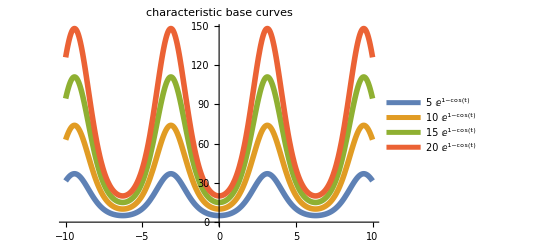

```mathematica
tab=Table[x[t]/.charBaseCurves1[[1]]/.{x0-> k},{k,5,20,5}]
Plot[Evaluate[tab],{t,-10,10},PlotStyle-> Thickness[0.01],PlotLegends-> Table[tab[[i]],{i,1,4}],PlotLabel-> "characteristic base curves"]
```

```mathematica
The Traffic Density function ρ(x,t) or the solution for the given initial value problem are given by:
```

```mathematica
eqn1=D[ρ[x,t],t]+x*Sin[t]*D[ρ[x,t],x]==0;
sol1=DSolve[{eqn1,ρ[x,0]==1 + 1/(1+x^2)},ρ[x,t],{x,t}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{ρ[x,t]→(2 ⅇ^2+ⅇ^(2 Cos[t]) x^2)/(ⅇ^2+ⅇ^(2 Cos[t]) x^2)}}

```mathematica
Hence ρ(x,t) is the traffic density function of the given initial value problem:
```

```mathematica
Plot3D[ρ[x,t]/.sol1,{x,-10,10},{t,-10,10},PlotLabel-> "Traffic Density Function"]
```

-Graphics3D-

```mathematica
Q2. Find the traffic density ρ(x,t) satisfying Subscript[ρ, t]+ e^t Subscript[ρ, x]=2ρ
with initial condition Subscript[ρ, 0](x)= 1 + Sin^2(x).
Plot the characteristic base curves and the traffic density function.
```

```mathematica
The characteristic base curve for the given initial value problem are given by:
```

```mathematica
charBaseCurves2=DSolve[{x'[t]==Exp[t],x[0]==x0},x[t],t]
```

{{x[t]→-1+ⅇ^t+x0}}

{3+ⅇ^t,7+ⅇ^t,11+ⅇ^t,15+ⅇ^t,19+ⅇ^t}

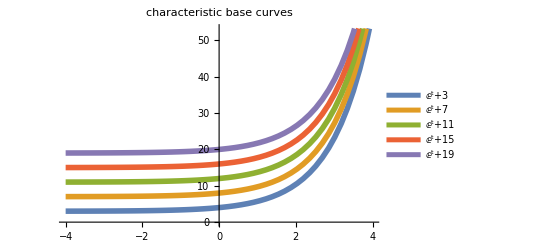

```mathematica
tab=Table[x[t]/.charBaseCurves2[[1]]/.{x0-> k},{k,4,20,4}]
Plot[Evaluate[tab],{t,-4,4},PlotStyle-> Thickness[0.01],PlotLegends-> Table[tab[[i]],{i,1,5}],PlotLabel-> "characteristic base curves"]
```

```mathematica
The Traffic Density function ρ(x,t) or the solution for the given initial value problem are given by:
```

```mathematica
eqn2=D[ρ[x,t],t]+Exp[t]*D[ρ[x,t],x]==2ρ[x,t];
sol2=DSolve[{eqn2,ρ[x,0]==1 + Sin[x]*Sin[x]},ρ[x,t],{x,t}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{ρ[x,t]→ⅇ^(2 t) (1+Sin[1-ⅇ^t+x]^2)}}

```mathematica
Hence ρ(x,t) is the traffic density function of the given initial value problem:
```

```mathematica
Plot3D[ρ[x,t]/.sol2,{x,-4,4},{t,-1,1},PlotLabel-> "Traffic Density Function"]
```

-Graphics3D-